```mathematica
ClearAll["Global`*"]
NotebookDelete[Cells[EvaluationNotebook[],GeneratedCell->True]]
```

## Parameters

### Input parameters

```mathematica
μr=125;
μf=125;
mH=125;
αs=0.11263992085801; (*μr=125 GeV*)
```

### Physical constants

```mathematica
Nc=3; (*number of colors*)
Nf=5; (*number of flavours*)
Gf=1.16637 10^-5; (*Fermi Constant*)
GevtoPb=3.8937966 10^8;
```

```mathematica
σ0=(αs^2 √2 Gf)/(576π); (*Born level cross-section σ0*)
CA=Nc;CF=(Nc^2-1)/(2Nc); (*Casimir Operators, see below Eq. 28*)
β0=1/6(11 CA-2Nf); (*Above Eq. 3.6*)
mH2=mH^2;
```

### Integration precision

```mathematica
WorkingPrecisionInteg=10; (*accuracy in significant number of digits*)
WorkingPrecisionPlot=10;
MaxErrorIncreasesInteg=10^3;
```

## Calculating dσ/dp_T(N)

### Required variables

```mathematica
tauh[pt2_,x_]:=x(√(1+pt2/mH2)-√(pt2/mH2))^2
sh[pt2_,x_]:=mH2/tauh[pt2,x]
QQmax[pt2_,x_]:=mH2+sh[pt2,x]-2 √(sh[pt2,x](pt2+mH2))
QQ[pt2_,x_,q_]:=q QQmax[pt2,x]
uh[pt2_,x_,q_]:=1/2(QQ[pt2,x,q]+mH2-sh[pt2,x]-√((sh[pt2,x]+mH2-QQ[pt2,x,q])^2-4sh[pt2,x](pt2+mH2)))
th[pt2_,x_,q_]:=1/2(QQ[pt2,x,q]+mH2-sh[pt2,x]+√((sh[pt2,x]+mH2-QQ[pt2,x,q])^2-4sh[pt2,x](pt2+mH2)))
```

### LO

```mathematica
JacytoQ2[pt2_,x_,q_]:=1/(√((sh[pt2,x]+mH2-QQ[pt2,x,q])^2-4 sh [pt2,x](pt2+mH2)))
```

```mathematica
ggg[pt2_,x_,q_]:=Nc((mH2^4+sh[pt2,x]^4+th[pt2,x,q]^4+uh[pt2,x,q]^4)/(th[pt2,x,q] uh[pt2,x,q] sh[pt2,x]))
dσdpt2dy[pt2_,x_,q_]:=GevtoPb σ0/sh[pt2,x] αs/(2π)ggg[pt2,x,q]JacytoQ2[pt2,x,q]*2(*times δ(Q^2)which is dealt with by the Jacobian*)(*Still no idea why we need this last factor 2*)
```

```mathematica
dσdpt2[pt2_,n_,q_]:=NIntegrate[dσdpt2dy[pt2,x,q] x^(n-1),{x,0,1},
MaxRecursion->Infinity,
Method->{GlobalAdaptive,MaxErrorIncreases->MaxErrorIncreasesInteg},
WorkingPrecision->WorkingPrecisionInteg]
dσdpt[pt_,n_,q_]:=2pt dσdpt2[pt^2,n,q]
```

#### Results

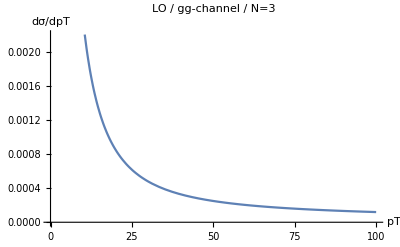

```mathematica
Plot[dσdpt[pt,3,0],{pt,1,100},PlotLabel->"LO / gg-channel / N=3",AxesLabel->{"pT","dσ/dpT"},PlotRange->{{0,Automatic},{0,Automatic}}]
```

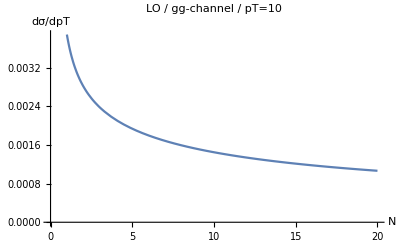

```mathematica
Plot[dσdpt[10,n,0],{n,1,20},PlotLabel->"LO / gg-channel / pT=10",AxesLabel->{"N","dσ/dpT"},PlotRange->{{0,Automatic},{0,Automatic}}]
```

### NLO term (only O[α_s^3] and only singular terms)

```mathematica
Jacytoq[pt2_,x_,q_]:=QQmax[pt2,x]/(√((sh[pt2,x]+mH2-QQ[pt2,x,q])^2-4 sh [pt2,x](pt2+mH2)))
za[pt2_,x_,q_]:=(-th[pt2,x,q])/(QQ[pt2,x,q]-th[pt2,x,q])
zb[pt2_,x_,q_]:=(-uh[pt2,x,q])/(QQ[pt2,x,q]-uh[pt2,x,q])
pgg[z_]:=Nc((1+z^4+(1-z)^4)/z)
```

Checks

```mathematica
ptt2=1^2;
Manipulate[Plot[{th[ptt2,x,q],uh[ptt2,x,q],Q2[ptt2,x,q],Jacytoq[ptt2,x,q]},{q,0,1},PlotLegends->{"th","uh","Q2","jac"}],{x,10^-10,1}]
```

#### plus distribution terms

```mathematica
a1factor[pt2_,x_,q_]:=(-th[pt2,x,q])/(za[pt2,x,q] QQmax[pt2,x])(Log[q]/q+Log[(QQmax[pt2,x] za[pt2,x,q])/(-th[pt2,x,q])] 1/q)
a1factor0[pt2_,x_,q_]:=(-th[pt2,x,0])/(za[pt2,x,0] QQmax[pt2,x])(Log[q]/q+Log[(QQmax[pt2,x] za[pt2,x,0])/(-th[pt2,x,0])] 1/q)
a1delta[pt2_,x_,q_]:=(-th[pt2,x,q])/(za[pt2,x,q] QQmax[pt2,x])1/2 Log[(QQmax[pt2,x] za[pt2,x,q])/(-th[pt2,x,q])]^2(* times δ(q)*)
b1factor[pt2_,x_,q_]:=(-th[pt2,x,q])/(za[pt2,x,q] QQmax[pt2,x])1/q
b1factor0[pt2_,x_,q_]:=(-th[pt2,x,0])/(za[pt2,x,0] QQmax[pt2,x])1/q

b1delta[pt2_,x_,q_]:=(-th[pt2,x,q])/(za[pt2,x,q] QQmax[pt2,x])Log[(QQmax[pt2,x] za[pt2,x,q])/(-th[pt2,x,q])](* times δ(q)*)
```

#### Terms in G_gg^(2s)

```mathematica
big1[pt2_,x_,q_]:=Nc^2/2 1/(sh[pt2,x] uh[pt2,x,q] th[pt2,x,q])((mH2^4+sh[pt2,x]^4+QQ[pt2,x,q]^4+uh[pt2,x,q]^4+th[pt2,x,q]^4)+za[pt2,x,q] zb[pt2,x,q](mH2^4+sh[pt2,x]^4+QQ[pt2,x,q]^4+(uh[pt2,x,q]/zb[pt2,x,q])^4+(th[pt2,x,q]/za[pt2,x,q])^4))
big2[pt2_,x_,q_]:=β0/2 Nc(1/(sh[pt2,x] uh[pt2,x,q] th[pt2,x,q])(mH2^4+sh[pt2,x]^4+za[pt2,x,q] zb[pt2,x,q] ((uh[pt2,x,q]/zb[pt2,x,q])^4+(th[pt2,x,q]/za[pt2,x,q])^4)))
a1[pt2_,x_,q_]:=1/(-th[pt2,x,q])pgg[za[pt2,x,q]]ggg[pt2,x,q]+za[pt2,x,q]/(-th[pt2,x,q])big1[pt2,x,q]
b1[pt2_,x_,q_]:=(za[pt2,x,q]/(-th[pt2,x,q]))(-Log[(QQ[pt2,x,q]+pt2)za[pt2,x,q]/-th[pt2,x,q]])big1[pt2,x,q]-(za[pt2,x,q]/(-th[pt2,x,q]))big2[pt2,x,q](*μF independent*)
```

#### Relevant parts of the cross section

```mathematica
dσdpt2dyqequal0[pt2_,x_,q_]:=(b1[pt2,x,0](b1delta[pt2,x,0]-b1factor0[pt2,x,q])+a1[pt2,x,0](a1delta[pt2,x,0]-a1factor0[pt2,x,q]))Jacytoq[pt2,x,0]
dσdpt2dyq[pt2_,x_,q_]:=(b1[pt2,x,q]b1factor[pt2,x,q]+a1[pt2,x,q]a1factor[pt2,x,q])Jacytoq[pt2,x,q]
```

```mathematica
dσdpt2dy[pt2_,x_,q_]:=GevtoPb σ0/sh[pt2,x](αs/(2π))^2(dσdpt2dyqequal0[pt2,x,q]+dσdpt2dyq[pt2,x,q])*2(*times δ(Q^2)which is dealt with by the Jacobian*)(*Still no idea why we need this last factor 2*)
```

```mathematica
dσdpt2[pt2_,n_]:=NIntegrate[dσdpt2dyqequal0[pt2,x,q] x^(n-1),{x,10^-7,1-10^-7},{q,0,1},
MaxRecursion->Infinity,
Method->{GlobalAdaptive,MaxErrorIncreases->MaxErrorIncreasesInteg},
WorkingPrecision->WorkingPrecisionInteg]
dσdpt[pt_,n_]:=2pt dσdpt2[pt^2,n]
```

### NLO term (δ(Q^2) term)

```mathematica
dσdpt2dy[pt2,Exp[Log[x]],q]//FullSimplify
```

(GevtoPb Nc (√(pt2/mH2)-√((mH2+pt2)/mH2))^6 x^3 (mH2^4+mH2^4/((√(pt2/mH2)-√((mH2+pt2)/mH2))^8 x^4)+1/16 (mH2+q (mH2-2 √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))+mH2/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))-mH2/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)-√(-(4 mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)+(-2 q √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))+((-1+q) (2 pt2 x+mH2 (1+x-2 √(pt2/mH2) √((mH2+pt2)/mH2) x)))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))^2))^4+1/16 (mH2+q (mH2-2 √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))+mH2/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))-mH2/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)+√(-(4 mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)+(-2 q √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))+((-1+q) (2 pt2 x+mH2 (1+x-2 √(pt2/mH2) √((mH2+pt2)/mH2) x)))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))^2))^4) αs σ0)/(mH2^2 π (-4 pt2 q √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)) x+mH2^2 q (1+x-2 √(pt2/mH2) √((mH2+pt2)/mH2) x)+mH2 (pt2+2 pt2 q x+2 (-1+2 √(pt2/mH2) √((mH2+pt2)/mH2)) q √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)) x)) √(-(4 mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x)+(-2 q √((mH2 (mH2+pt2))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))+((-1+q) (2 pt2 x+mH2 (1+x-2 √(pt2/mH2) √((mH2+pt2)/mH2) x)))/((√(pt2/mH2)-√((mH2+pt2)/mH2))^2 x))^2))